```mathematica
Datax = Table[0.5+n*0.06, {n, 0, 24} ]
Datay = {2.02, 1.76786, 1.62903, 1.45588, 1.36486, 1.2375, 1.17442, 1.07609, 1.03061, 0.951923, 0.918182,0.853448, 0.827869, 0.773438, 0.753731, 0.707143, 0.691781, 0.651316, 0.639241, 0.603659, 0.594118, 0.5625, 0.554945, 0.526596, 0.520619}
data = Transpose[{Datax, Datay}]
```

{0.5,0.56,0.62,0.68,0.74,0.8,0.86,0.92,0.98,1.04,1.1,1.16,1.22,1.28,1.34,1.4,1.46,1.52,1.58,1.64,1.7,1.76,1.82,1.88,1.94}

{2.02,1.76786,1.62903,1.45588,1.36486,1.2375,1.17442,1.07609,1.03061,0.951923,0.918182,0.853448,0.827869,0.773438,0.753731,0.707143,0.691781,0.651316,0.639241,0.603659,0.594118,0.5625,0.554945,0.526596,0.520619}

{{0.5,2.02},{0.56,1.76786},{0.62,1.62903},{0.68,1.45588},{0.74,1.36486},{0.8,1.2375},{0.86,1.17442},{0.92,1.07609},{0.98,1.03061},{1.04,0.951923},{1.1,0.918182},{1.16,0.853448},{1.22,0.827869},{1.28,0.773438},{1.34,0.753731},{1.4,0.707143},{1.46,0.691781},{1.52,0.651316},{1.58,0.639241},{1.64,0.603659},{1.7,0.594118},{1.76,0.5625},{1.82,0.554945},{1.88,0.526596},{1.94,0.520619}}

```mathematica
(* 1 task*)
p24[x_]:=InterpolatingPolynomial[data, x];
```

```mathematica
a = 0.5
b = 1.94

evenx = Select[Range[24], EvenQ];
dataEven = data[[evenx]];
p12[x_]:= InterpolatingPolynomial[dataEven, x];

thirdx = Range[1, 24, 3];
datath = data[[thirdx]];
p8[x_]:= InterpolatingPolynomial[datath, x];

fourthx = Range[1, 24, 4];
dataf = data[[fourthx]];
p6[x_]:= InterpolatingPolynomial[dataf, x];
```

0.5

1.94

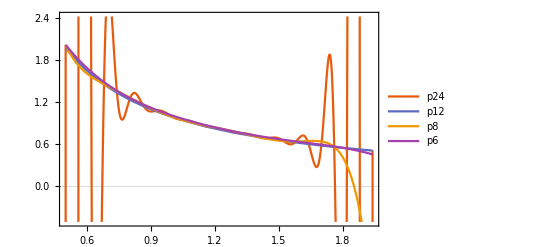

Grid[{xj,f(xj),p24(xj),error},{{0.5,2.02,2.02,0.},{0.56,1.76786,1.76786,2.22045×10^-16},{0.62,1.62903,1.62903,2.22045×10^-16},{0.68,1.45588,1.45588,0.},{0.74,1.36486,1.36486,0.},{0.8,1.2375,1.2375,2.22045×10^-16},{0.86,1.17442,1.17442,0.},{0.92,1.07609,1.07609,2.22045×10^-16},{0.98,1.03061,1.03061,2.22045×10^-16},{1.04,0.951923,0.951923,1.11022×10^-16},{1.1,0.918182,0.918182,1.11022×10^-16},{1.16,0.853448,0.853448,1.11022×10^-16},{1.22,0.827869,0.827869,2.22045×10^-16},{1.28,0.773438,0.773438,1.11022×10^-16},{1.34,0.753731,0.753731,1.11022×10^-16},{1.4,0.707143,0.707143,1.11022×10^-16},{1.46,0.691781,0.691781,0.},{1.52,0.651316,0.651316,0.},{1.58,0.639241,0.639241,1.11022×10^-16},{1.64,0.603659,0.603659,1.11022×10^-16},{1.7,0.594118,0.594118,1.11022×10^-16},{1.76,0.5625,0.5625,0.},{1.82,0.554945,0.554945,0.},{1.88,0.526596,0.526596,0.},{1.94,0.520619,0.520619,0.}},Frame→All,ItemStyle→{{xj,f(xj),p24(xj),error}}]

```mathematica
Plot[{p24[x],p12[x],p8[x],p6[x]}, {x, a, b}, 
PlotLegends->{"p24", "p12", "p8", "p6"}, PlotTheme->"Scientific"]
errors24 = Abs[(p24[x] /. x -> #)-#2] & @@@ data;
errors12 = Abs[(p12[x] /. x -> #)-#2] & @@@ data;
errors8 = Abs[(p8[x] /. x -> #)-#2] & @@@ data;
errors6 = Abs[(p6[x] /. x -> #)-#2] & @@@ data;

Grid[{"xj", "f(xj)", "p24(xj)", "error"},Transpose[{Datax, Datay, (p24[x] /. x->Datax), errors24}], Frame->All, ItemStyle->{{"xj", "f(xj)", "p24(xj)", "error"}}]
```

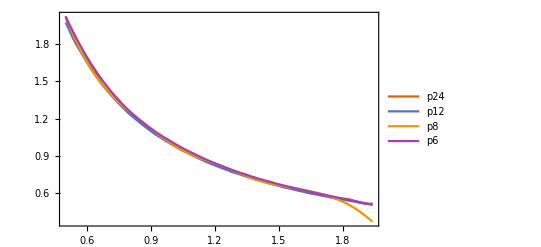

```mathematica
(*Task 2*)
sAll = Interpolation[data, Method->"Spline"];
sEven = Interpolation[dataEven, Method->"Spline"];
sThird = Interpolation[datath, Method->"Spline"];
sFourth = Interpolation[dataf, Method->"Spline"];
Plot[{sAll[x],sEven[x],sThird[x],sFourth[x]}, {x, a, b}, 
PlotLegends->{"p24", "p12", "p8", "p6"}, PlotTheme->"Scientific"]
```

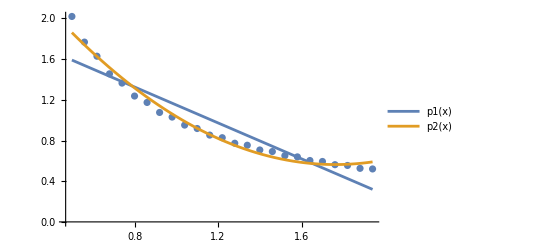

{0.532533,0.0679517}

```mathematica
(*task3*)
Clear[x];
p1= Fit[data, {1, x}, x];
p2= Fit[data, {1, x, x^2}, x];
err1 = MapThread[(p1 /. x -> #1)- #2 &, {Datax, Datay}];
err2 = MapThread[(p2 /. x -> #1)- #2 &, {Datax, Datay}];

sse1 =Total[err1^2];
sse2 =Total[err2^2];

Clear[x];
Show[
ListPlot[data],
Plot[{p1, p2}, {x, a, b},PlotLegends->{"p1(x)","p2(x)"}]]
{sse1, sse2}
```

```mathematica
(*tas5*)
f1 = ConstantArray[0., 25];
h = (Last[Datax]-First[Datay])/(25-1);

f1[[1]]=(-3 Datay[[1]]+ 4 Datay[[2]]-Datay[[3]])/(2h);
Do[f1[[j]]=(Datay[[j+1]]-Datay[[j-1]])/(2h), {j, 2, 25-1}];
f1[[25]] = (3 Datay[[25]]-4Datay[[25-1]]+Datay[[25-2]])/(2h);

f2 = ConstantArray[0., 25];
(*f2[[1]]=(2Datay[[1]]-5 Datay[[2]]+4Datay[[3]]-Datay[[4]])/h^2;*)
Do[f2[[j]]=(Datay[[j+1]]-2Datay[[j]]+Datay[[j-1]])/h^2, {j, 2, 25-1}];
(*f2[[25]] = (2 Datay[[25]]-5Datay[[25-1]]+4Datay[[25-2]]-Datay[[25-3]])/h^2;*)

TableForm[Transpose[{Datax, f1}], TableHeadings->{None, {"xj", "f'(xj)"}}]
TableForm[Transpose[{Datax, f2}],TableHeadings->{None, {"xj", "f''(xj)"}}]
```

xj | f'(xj)
0.5 | 92.6385
0.56 | 58.6455
0.62 | 46.797
0.68 | 39.6255
0.74 | 32.757
0.8 | 28.566
0.86 | 24.2115
0.92 | 21.5715
0.98 | 18.625
1.04 | 16.8642
1.1 | 14.7712
1.16 | 13.547
1.22 | 12.0015
1.28 | 11.1207
1.34 | 9.94425
1.4 | 9.2925
1.46 | 8.37405
1.52 | 7.881
1.58 | 7.14855
1.64 | 6.76845
1.7 | 6.17385
1.76 | 5.87595
1.82 | 5.3856
1.88 | 5.1489
1.94 | -1.5627

xj | f''(xj)
0.5 | 0.
0.56 | 10197.9
0.62 | -3088.8
0.68 | 7391.7
0.74 | -3270.6
0.8 | 5785.2
0.86 | -3172.5
0.92 | 4756.5
0.98 | -2988.63
1.04 | 4045.14
1.1 | -2789.37
1.16 | 3523.95
1.22 | -2596.68
1.28 | 3125.16
1.34 | -2419.29
1.4 | 2810.34
1.46 | -2259.27
1.52 | 2555.1
1.58 | -2115.63
1.64 | 2343.69
1.7 | -1986.93
1.76 | 2165.67
1.82 | -1871.46
1.88 | 2013.48
1.94 | 0.

```mathematica
(*task6*)
midpoints = Table[(Datax[[j]] +Datax[[j+1]])/2, {j, 1, 25-1}];

Imidh = h Total[sAll /@ midpoints];
Itraph = (h/2)(Datay[[1]]+2Total[Datay[[2 ;; 25-1]]] + Datay[[25]]);
Isemph = If[EvenQ[25-1], (h/3)(Datay[[1]]+Datay[[25]]+4Total[Datay[[2 ;; 25-1 ;; 2]]]+2Total[Datay[[3 ;; 25-2 ;; 2]]]),
Missing["nope"]
];
```

```mathematica
x2 = Datax[[;; ;; 2]];
f2h = Datay[[;; ;; 2]];
n2 = Length[x2];
h2 = 2h;

midpoints2 = Table[(x2[[j]]+x2[[j+1]])/2, {j, 1, n2-1}];
Imid2h = h2 Total[sAll /@ midpoints2];
Itrap2h = (h2/2)(f2h[[1]]+2Total[f2h[[2 ;; n2-1]]] + f2h[[n2]]);
Isemp2h = If[EvenQ[25-1], (h2/3)(f2h[[1]]+f2h[[n2]]+4Total[f2h[[2 ;; n2-1 ;; 2]]]+2Total[f2h[[3 ;; n2-2 ;; 2]]]),
Missing["nope"]
];
```

```mathematica
errmid = (Imidh-Imid2h)/3.;
errmtrap = (Itraph-Itrap2h)/3.;
errsimps = If[Isemph === Missing["nope"] || Isemp2h === Missing["nope"], Missing["nope"], (Isemph-Isemp2h)/15.];

Imidrich = Imidh+errmid;
Itraprich = Itraph+errmtrap;
Isemprich = If[errsimps === Missing["nope"], Missing["nope"], Isemph+errsimps];

Grid[{
{"Метод", "I(h)", "I(2h)", "Runge error", "Richardson"},
{"средние", Imidh, Imid2h, errmid, Imidrich},
{"трапеции", Itraph, Itrap2h, errmtrap, Itraprich},
{"Симпсона", Isemph, Isemp2h, errsimps, Isemprich}}, Frame->All]
```

Метод | I(h) | I(2h) | Runge error | Richardson
средние | -0.0752134 | -0.074449 | -0.000254777 | -0.0754681
трапеции | -0.0753882 | -0.0763273 | 0.000313048 | -0.0750751
Симпсона | -0.0750751 | -0.0760829 | 0.0000671835 | -0.0750079